```mathematica
Exit[]
```

```mathematica
str[x_]:=Table[x[[i*n/1000]],{i,1,1000}]
```

```mathematica
σ=0.2;r=0.04;
```

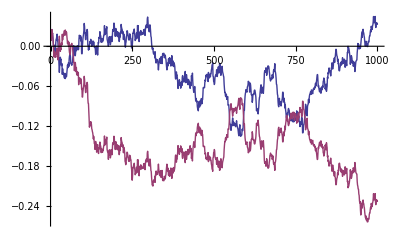

```mathematica
n=5000;dW=RandomReal[NormalDistribution[],{n}]/Sqrt[n];W=Join[{0},Accumulate[dW]];
S=Table[Exp[(r-σ^2/2)(t-1)/n+σ W[[t]]],{t,1,n+1}];
q[x_]:=-2 UnitStep[x]+1;
P={0};
For[i=1,i<n+1,i++,
AppendTo[P,P[[i]]-(-2 UnitStep[P[[i]]]+1)(S[[i+1]]-S[[i]])];
]
ListLinePlot[{str[P],str[S]-1}]
```

```mathematica
P={0};q[x_]:=-2 UnitStep[x]+1;n=5000;
For[j=1,j<2,j++,
dW=RandomReal[NormalDistribution[],{n}]/Sqrt[n];
W=Join[{0},Accumulate[dW]];
S=Table[Exp[(r-σ^2/2)(t-1)/n+σ W[[t]]],{t,1,n+1}];
G=0;
For[i=1,i<n+1,i++,
G-=(-2 UnitStep[G]+1)(S[[i+1]]-S[[i]]);
]]
```